```mathematica
Clear[ϵ0]
```

```mathematica
(* Just simply confirming the Laplacian in polar coordinates *)
```

```mathematica
FullSimplify[Laplacian[f[r,θ],{r,θ},"Polar"]]
```

(f^(0,2)[r,θ]+r f^(1,0)[r,θ])/r^2+f^(2,0)[r,θ]

```mathematica
(* Polar Laplacian of the potential due to point charge in spherical coordinates *)
```

```mathematica
FullSimplify[D[q/(4π ϵ0)/Sqrt[r^2+2R^2-2R r(Sin[θ]+Cos[θ])],{r,2}]+1/r D[q/(4π ϵ0)/Sqrt[r^2+2R^2-2R r(Sin[θ]+Cos[θ])],r]+1/r^2 D[q/(4π ϵ0)/Sqrt[r^2+2R^2-2R r(Sin[θ]+Cos[θ])],{θ,2}]]
```

q/(4 π ϵ0 (r^2+2 R^2-2 r R (Cos[θ]+Sin[θ]))^(3/2))

```mathematica
(* And here is the plot showing the charge density in space: resembles dirac delta but not exactly (not even approximately)!! *)
```

```mathematica
Block[
{ϵ,R,q,r,θ},
ϵ=2.1*10^(-2);R=10^(-7);q=1.6*10^(-19);
Plot3D[(q/(4 π(r^2+2 R^2-2 r R (Cos[θ]+Sin[θ]))^(3/2)))/.{r->Sqrt[x^2+y^2],θ->ArcTan[x,y]},
{x,R-ϵ R,R+ϵ R},{y,R-ϵ R,R+ϵ R},PlotRange->All,AxesLabel->{"x (in m)","y (in m)","ρ[x,y] (in C.m^(-3))"}]
]
```

-Graphics3D-

```mathematica
(* And with this, the FEM gives the following potential field from an electron .... *)
```

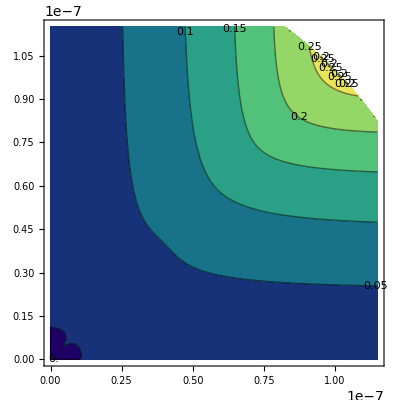

```mathematica
Block[
{potent,ϕ0,f,ϵ,ϵ0,R,q},
ϵ=2.1*10^(-2);R=10^(-7);q=-1.6*10^(-19);ϵ0=8.85*10^(-12);ϕ0=0;
potent=NDSolveValue[{Laplacian[f[r,θ],{r,θ},"Polar"]==(q/(4 π ϵ0 (r^2+2 R^2-2 r R (Cos[θ]+Sin[θ]))^(3/2))),f[r,0]==ϕ0,f[r,π/2]==ϕ0},f[r,θ],{r,0,Sqrt[2]R},{θ,0,π/2}];
ContourPlot[potent/.{r->Sqrt[x^2+y^2],θ->ArcTan[x,y]},{x,0,1.15R},{y,0,1.15R},ColorFunction->"BlueGreenYellow",ContourLabels->All]
]
```

```mathematica
(* And with this, the FEM gives the following potential field from a proton .... *)
```

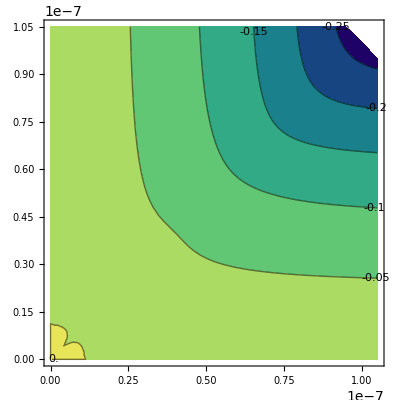

```mathematica
Block[
{potent,ϕ0,f,ϵ,ϵ0,R,q},
ϵ=2.1*10^(-4);R=10^(-7);q=1.6*10^(-19);ϵ0=8.85*10^(-12);ϕ0=0;
potent=NDSolveValue[{Laplacian[f[r,θ],{r,θ},"Polar"]==(q/(4 π ϵ0 (r^2+2 R^2-2 r R (Cos[θ]+Sin[θ]))^(3/2))),f[r,0]==ϕ0,f[r,π/2]==ϕ0},f[r,θ],{r,0,Sqrt[2]R},{θ,0,π/2}];
ContourPlot[potent/.{r->Sqrt[x^2+y^2],θ->ArcTan[x,y]},{x,0,1.05R},{y,0,1.05R},ColorFunction->"BlueGreenYellow",ContourLabels->All]
]
```

```mathematica
(* And here is the matched asymptotics from an electron, I will redocument all of the code below some time later ... *)
```

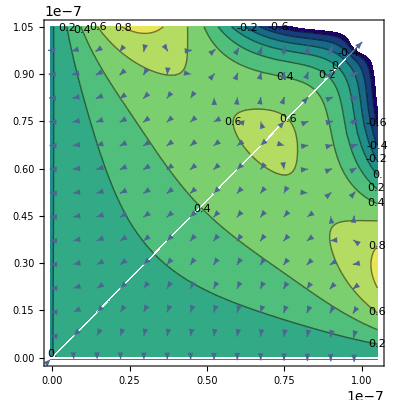

```mathematica
With[
{ϵ=5*10^(-3),ϵ0=8.85*10^(-12),R=10^(-7),q=-1.6*10^(-19),M=10,n=1000},
Show[
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+
If[
0≤ArcTan[x,y]<π/4,
q/(4 Sqrt[2]π ϵ0 R)1/n(1-Sqrt[x^2+y^2]/R)^n Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-q Log[2]/(16 n π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]),{m,1,M}]
]
]
+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)
,{x,-ϵ R,1.05R},{y,-ϵ R,1.05R},ColorFunction->"BlueGreenYellow",ContourLabels->All
],
VectorPlot[{(q (-R+x))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+q/(4 Sqrt[2]π ϵ0 R)Sum[4^-m m ((√(x^2+y^2))/R)^m Binomial[2 m,m] (-((x+y)/(√(x^2+y^2)))^m (x^2+y^2)+(x+y) Sec[(m π)/(4+2 ϵ)] (x Cos[(m π)/(4+2 ϵ)-m ArcTan[x,y]]-y Sin[(m π)/(4+2 ϵ)-m ArcTan[x,y]]))/((x+y) (x^2+y^2)),{m,1,M}]+If[0≤ArcTan[x,y]<π/4,q/(4 Sqrt[2]n π ϵ0 R)Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Tan[(m+1)π/(4+2ϵ)]-1)(1/((x^2+y^2) (-R+√(x^2+y^2)))((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n (-y (n √(x^2+y^2)+m (-R+√(x^2+y^2))) Cos[m ArcTan[x,y]]+m x (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]])),{m,1,M}],If[ArcTan[x,y]==π/4,-q Log[2]/(16 n π ϵ0 R)Sum[(-(4^-m m x ((√(x^2+y^2))/R)^m)/(x^2+y^2))Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],Sum[-1/(n π R (x^2+y^2) (-R+√(x^2+y^2)) ϵ0)2^(-9/2-2 m) (1+m) q ((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (If[Mod[m,2]==0,Sec[(m π)/2],0] (x (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Cos[m ArcTan[x,y]]+m y (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]])+If[Mod[m,2]==1,Csc[(m π)/2],0] (-m y (-R+√(x^2+y^2)) Cos[m ArcTan[x,y]]+x (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Sin[m ArcTan[x,y]])) (-1+Sin[((1+m) π)/(2+ϵ)]+Cos[((1+m) π)/(2+ϵ)] Tan[((1+m) π)/(4+2 ϵ)]),{m,1,M}]]],
q/(4 Sqrt[2]π ϵ0 R)Sum[1/((x+y) (x^2+y^2))4^-m m ((√(x^2+y^2))/R)^m Binomial[2 m,m] (-((x+y)/(√(x^2+y^2)))^m (x^2+y^2)+(x+y) (y Cos[m ArcTan[x,y]]-x Sin[m ArcTan[x,y]]+(x Cos[m ArcTan[x,y]]+y Sin[m ArcTan[x,y]]) Tan[(m π)/(4+2 ϵ)])),{m,1,M}]+If[0≤ArcTan[x,y]<π/4,q/(4 Sqrt[2]n π ϵ0 R)Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Tan[(m+1)π/(4+2ϵ)]-1)(-((((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n (x (n √(x^2+y^2)+m (-R+√(x^2+y^2))) Cos[m ArcTan[x,y]]+m y (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]]))/((x^2+y^2) (-R+√(x^2+y^2))))),{m,1,M}],If[ArcTan[x,y]==π/4,-q Log[2]/(16 n π ϵ0 R)Sum[(-(4^-m m y ((√(x^2+y^2))/R)^m)/(x^2+y^2))Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],Sum[-1/(n π R (x^2+y^2) (-R+√(x^2+y^2)) ϵ0)2^(-9/2-2 m) (1+m) q ((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (If[Mod[m,2]==0,Sec[(m π)/2],0] (y (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Cos[m ArcTan[x,y]]+m x (R-√(x^2+y^2)) Sin[m ArcTan[x,y]])+If[Mod[m,2]==1,Csc[(m π)/2],0] (m x (-R+√(x^2+y^2)) Cos[m ArcTan[x,y]]+y (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Sin[m ArcTan[x,y]])) (-1+Sin[((1+m) π)/(2+ϵ)]+Cos[((1+m) π)/(2+ϵ)] Tan[((1+m) π)/(4+2 ϵ)]),{m,1,M}]]]+(q (-R+y))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)
},{x,-ϵ R,1.05R},{y,-ϵ R,1.05R},VectorScale->{0.05,1,Automatic},PlotTheme->Automatic]
]
]
```